# Wolfram Mathematica Knowledge Book

## Chapter 1: Core Objects

Symbols

### Define

#### Symbolize a notation:

```mathematica
Needs["Notation`"]
Symbolize[Subscript[d, 1]]
(*Notation Palette*)
```

#### Define Symbols

```mathematica
=, Set, :=, SetDelayed

SetAttributes[f,HoldAll], Attributes[f]={HoldAll}
```

#### Show definition :

```mathematica
Definition[symbol]
Attributes[symbol]
```

#### Attributes :

```mathematica
tutorial/Attributes:
Listable,
```

```mathematica
SetAttributes[f, Orderless]
 ClearAttributes[symbol, attribute]
```

### Clean

#### Clear values, definitions, attributes, messages, and defaults associated with symbols

```mathematica
ClearAll[symbal]
ClearAll["x*"]
ClearAll["Context`s*"]
```

#### Clear Values

```mathematica
Clear[symbal]
symbal = .
```

#### Clear Attributes

```mathematica
ClearAttributes[f,Listable]
Attributes[f]=Complement[Attributes[f],{HoldFirst,NHoldFirst}]
```

#### Clear Symbols

```mathematica
Remove[symbol]
```

Numbers

## Categories:

```mathematica
Integer, Rational, Real, Complex
```

## Precision & Accuracy

```mathematica
Precision as providing a measure of the relative size of this uncertainty. 
Accuracy gives a measure of the absolute size of the uncertainty
```

```mathematica
$MachinePrecision 
64 binary digits (IEEE double floats) :
one for the sign, eleven for the exponent, and fifty-two for the mantissa 
$MachinePrecision =  (64-11)log[10,2]

Absolute Uncertainty δ = |x|*10^-p; 
Pricision p = - Log[10, δ/(|x|)], 
Accuracy a = -Log[10, δ]=p-Log[10, |x|]
```

```mathematica
Aproximate Result involves None exact numbers.
Exact Result involves Interger, Rational arithmatic expression.
```

```mathematica
Precision, Accuracy
SetPrecision, 
$MinPrecision, $MaxPrecision
```

```mathematica
Block[{$MinPrecision = 30, $MaxPrecision = 30}, values = NestList[4#(1-#) &,N[3/10, 30], 60]}
```

## BaseForm

```mathematica
BaseForm[expr, base]
2^^101101010101
```

## Measure and Unit

```mathematica
Quantity[2,"Feet"]
Quantity[2,"Feet"]+Quantity[3,"Meters"]
UnitConvert[%,"Meters"] 
Quantity[7,"days"]+Quantity[2,"weeks"]
```

## Built - in Functions

```mathematica
Head, FromDigits, NumberForm
```

```mathematica
IntegerDigits, RealDigits, IntegerString, IntegerString
```

```mathematica
Interval, IntervalUnion, IntervalMemberQ, IntervalIntersection
```

```mathematica
Floor, Ceiling, Round, 
Rationalize,
```

```mathematica
AccountingForm, , PaddedForm, EngineeringForm , ScientificForm, 
DigitBlock, NumberPadding ,
```

```mathematica
NumberFormat
```

### Complex Numbers

```mathematica
Re, Im, Conjugate, Abs, Arg,
```

Sequences

## list

### Generator

```mathematica
Table, Range, {}, List[],
```

### Display

```mathematica
TableForm, MatrixForm, Grid, ArrayPlot, AdjacencyGraph
```

### Operator

```mathematica
PrependTo
AppendTo
list⟦3⟧ = 3
```

```mathematica
Prepend,
Append,
Insert
ReplacePart
Delete
```

```mathematica
Part, [[]], ⟦ ⟧,
First, Rest, Last, Most, Take, Drop, Select, Cases, 
Span, ;;,
Position, Count, MemberQ, FreeQ,
```

```mathematica
Length, Dimensions, ArrayDepth, Depth, Level
```

```mathematica
Flatten, FlattenAt, Join, 
Sort, RotateLeft, RotateRight, Reverse, Partition, SortBy,
Ordering,
```

```mathematica
Union, ∪, Intersection, ∩, Complement, Subsets, DeleteDuplicates, SubsetQ, MemberQ,
```

```mathematica
Total, Sum, Accumulate, Min, Max, 
Row, Column,
```

```mathematica
ListConvolve, ListCorrelate
```

## String

### Generator

```mathematica
Table[Unique["x"], {7}]
ToString, CharacterRange, FromCharacterCode, ToCharacterCode,ToUpperCase
```

### Operate

```mathematica
StringQ, LetterQ, LowerCaseQ, SameQ, OrderedQ, StringMatchQ, StringFreeQ,
FullForm, OutputForm,
Head, StringLength,
<>, StringJoin, StringReverse, StringRiffle
StringTrim, StringDrop, StringPosition, 
StringTake, StringReplace, StringSplit
StringCases,


StringCount,

Characters, Hash,
```

### StringExpression(~~)

```mathematica
LetterCharacter, DigitCharacter, NumberString, WordBoundary, StartOfString, EndOfString 
StartOfLine, EndOfLine,
```

```mathematica
StringExpression, ~~, 
StringMatchQ, 
StringMatchQ["abccde", __ ~~ s_ ~~ s_ ~~ __]
StringCases
```

### Regular Expression

```mathematica
StringMatchQ["a", RegularExpression["."D]]
"."
"[a-z]"
"a*"
"a+"
"a?"
"a.*"
"\\d"
"\\D"
"\\s"
"\\S"
"\\w"
"\\W"
"[[:named:]]"
"[^[:named:]]"
"\\b\\w{16,18}\\b"
```

```mathematica
StringCases[text, WordBoundary ~~ RegularExpression["\\w{16,18}"]~~ WordBoundary]
StringReplace[words, WordBoundary ~~ a_ :> ToLowerCase[a]]
StringReplace[words, RegularExpression["\\b(\\w)"] :> ToLowerCase["$1"]]
StringReplace[words, RegularExpression["\\b(\\w)(\\w)"] :> ToLowerCase["$1" ~~ ToUpperCase["$2"]]
```

### Texting

```mathematica
DictionaryLookup, WordData,
```

```mathematica
Print,
```

```mathematica
$CharacterEncoding 
 $SystemCharacterEncoding
 $CharacterEncodings
```

## Generic Sequence

```mathematica
Sort,
SortBy,
Reverse,
```

```mathematica
Case,
_Integer, _Real, _String
```

```mathematica
Select, First, Rest,
```

```mathematica
Select[Cases[cleanedNewScores,{_,_String,_Integer}],selectFun2]
Select[Flatten[cleanedNewScores],NumberQ]
```

```mathematica
Nothing
data/.{"Missing"} -> Nothing
```

Data Sets

## Associate

### Constructor

```mathematica
Data = Association[{"Cliff"->99,"Kelvin"->96,"Michael"->95}] 
Normal[Dataset[scoreAssoc]]
Data["tag"]
```

```mathematica
AssociationThread
```

```mathematica
Keys,
Values,
```

## DataSet

### Constructor

```mathematica
Dataset[data]
```

### Operate

```mathematica
DeleteMissing
```

Graphics

## Plotting

### Plot/Plot3D

#### Plot by example:

```mathematica
(* usage *)
Plot[f,{x,Subscript[x, min],Subscript[x, max]}]
Plot[{Subscript[f, 1],Subscript[f, 2],…},{x,Subscript[x, min],Subscript[x, max]}]
Plot[{…,w[Subscript[f, i]],…},…]
Plot[…,{x}∈reg]
```

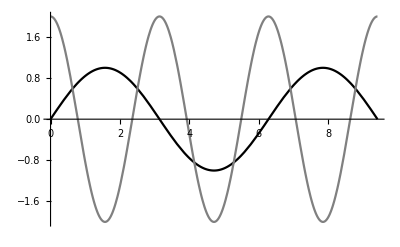

```mathematica
Plot[{Sin[x],2Cos[2x]},{x,0,3π},PlotStyle->{GrayLevel[0],GrayLevel[0.5]}]
```

```mathematica
gr=Plot[Sin[x],{x,0,π}];
Show[{gr, gr /. {x_?NumberQ, y_?NumberQ} :> {y, x}, 
Graphics[{Dashed, Line[{{0, 0}, {π, π}}]}], 
PlotRange -> All, AspectRatio -> Automatic]
```

#### Plot3D by example

```mathematica
(* usage *)
Plot3D[f,{x,Subscript[x, min],Subscript[x, max]},{y,Subscript[y, min],Subscript[y, max]}]
Plot3D[{Subscript[f, 1],Subscript[f, 2],…},{x,Subscript[x, min],Subscript[x, max]},{y,Subscript[y, min],Subscript[y, max]}]
Plot3D[…,{x,y}∈reg]
```

```mathematica
Plot3D[Sin[x+Cos[y]],{x,-4π,4π},{y,-4π,4π}]
```

### ListPlot/ListPlot3D

```mathematica
ListPlot
ListLinePlot

ListLinePlot[{1, 4, 9, 16, 25}, Mesh -> All, Filling -> Axis, AxesOrigin -> {1, 0}]
```

```mathematica
ListPolarPlot
ListStepPlot
```

```mathematica
ListLogPlot
ListLogLogPlot
ListLogLinearPlot

Manipulate[lplot[data], {lplot,{ListPlot, ListLinePlot, ListLogPlot,ListLogLogPlot}}, 
Initialization :> (data={1,4,9,16,25})]
```

```mathematica
ListPointPlot3D
ListPlot3D
ListSurfacePlot3D
```

```mathematica
ListDensityPlot
ListDensityPlot3D
```

```mathematica
ListContourPlot
ListContourPlot3D
```

```mathematica
ListVectorDensityPlot
ListVectorPlot
ListVectorPlot3D
```

```mathematica
ListSliceContourPlot3D
ListSliceDensityPlot3D
ListSliceVectorPlot3D
```

```mathematica
ListStreamDensityPlot
ListStreamPlot
```

### ContourPlot/ContourPlot3D

#### ContourPlot by Example

```mathematica
(* Usage *)
ContourPlot[f,{x,Subscript[x, min],Subscript[x, max]},{y,Subscript[y, min],Subscript[y, max]}]
ContourPlot[f==g,{x,Subscript[x, min],Subscript[x, max]},{y,Subscript[y, min],Subscript[y, max]}]
ContourPlot[{Subscript[f, 1]==Subscript[g, 1],Subscript[f, 2]==Subscript[g, 2],…},{x,Subscript[x, min],Subscript[x, max]},{y,Subscript[y, min],Subscript[y, max]}]
ContourPlot[…,{x,y}∈reg]
```

```mathematica
ContourPlot[Sin[x+Cos[y]],{x,-4π,4π},{y,-4π,4π}]
```

#### ContourPlot3D by Example

```mathematica
(* Usage *)
ContourPlot3D[f==g,{x,Subscript[x, min],Subscript[x, max]},{y,Subscript[y, min],Subscript[y, max]},{z,Subscript[z, min],Subscript[z, max]}]
ContourPlot3D[f,{x,Subscript[x, min],Subscript[x, max]},{y,Subscript[y, min],Subscript[y, max]},{z,Subscript[z, min],Subscript[z, max]}]
```

```mathematica
Manipulate[
ContourPlot3D[x^2+y^2+z^2==r,{x,-2,2},{y,-2,2},{z,-2,2}, 
ColorFunction->Function[{x,y,z},Hue[r]]],
{r, 1, 8}]
```

### DensityPlot/DensityPlot3D

```mathematica
DensityPlot[f,{x,Subscript[x, min],Subscript[x, max]},{y,Subscript[y, min],Subscript[y, max]}]
DensityPlot[f,{x,y}∈reg]
```

```mathematica
DensityPlot3D[f,{x,Subscript[x, min],Subscript[x, max]},{y,Subscript[y, min],Subscript[y, max]},{z,Subscript[z, min],Subscript[z, max]}] 
DensityPlot3D[f,{x,y,z}∈reg]
```

### ParametricPlot/ParametricPlot3D

#### ParametricPlot by example

```mathematica
(* Usage *)
ParametricPlot[{Subscript[f, x],Subscript[f, y]},{u,Subscript[u, min],Subscript[u, max]}]
ParametricPlot[{{Subscript[f, x],Subscript[f, y]},{Subscript[g, x],Subscript[g, y]},…},{u,Subscript[u, min],Subscript[u, max]}]
ParametricPlot[{Subscript[f, x],Subscript[f, y]},{u,Subscript[u, min],Subscript[u, max]},{v,Subscript[v, min],Subscript[v, max]}]
ParametricPlot[{{Subscript[f, x],Subscript[f, y]},{Subscript[g, x],Subscript[g, y]},…},{u,Subscript[u, min],Subscript[u, max]},{v,Subscript[v, min],Subscript[v, max]}]
ParametricPlot[…,{u,v}∈reg]
```

```mathematica
Manipulate[
ParametricPlot[{t+Sin[m t], t+Sin[n t]},{t, -π, π}],
{m,1,5},{n, 1, 5}]
```

```mathematica
ParametricPlot[
{{2Cos[t],2Sin[t]},
{2Cos[t],Sin[t]},
{Cos[t],2Sin[t]},
{Cos[t],Sin[t]}},
{t,0,2Pi},
PlotLegends->"Expressions"]
```

#### ParametricPlot3D by example

```mathematica
(* Usage *)
ParametricPlot3D[{Subscript[f, x],Subscript[f, y],Subscript[f, z]},{u,Subscript[u, min],Subscript[u, max]}]
ParametricPlot3D[{Subscript[f, x],Subscript[f, y],Subscript[f, z]},{u,Subscript[u, min],Subscript[u, max]},{v,Subscript[v, min],Subscript[v, max]}]
ParametricPlot3D[{{Subscript[f, x],Subscript[f, y],Subscript[f, z]},{Subscript[g, x],Subscript[g, y],Subscript[g, z]}…}…]
ParametricPlot3D[…,{u,v}∈reg]
```

```mathematica
ParametricPlot3D[
{Sin[u],Cos[u],u/10},
{u,0,20}]
```

```mathematica
ParametricPlot3D[
{
{4+(3+Cos[v]) Sin[u], 4+(3+Cos[v]) Cos[u], 4+Sin[v]},
{8+(3+Cos[v]) Cos[u], 3+Sin[v], 4+(3+Cos[v]) Sin[u]}
},
{u,0,2Pi},{v,0,2Pi},
PlotStyle->{Red,Green}]
```

### PolarPlot/SphericalPlot3D/RevolutionPlot3D

### Log Plot

```mathematica
LogPlot
LogLinearPlot
LogLogPlot
```

```mathematica
ListLogPlot
ListLogLinearPlot
ListLogLogPlot
```

### NumberLinePlot/RegionPlot/RegionPlot3D

### VectorPlot/VectorPlot3D

#### VectorPlot by example

```mathematica
VectorPlot[{1,Cos[y/x]},{x, -2π,2π},{y, -2π,2π},VectorPoints -> 25, Axes->Automatic,AxesOrigin->{0,0}]
```

### StreamPlot/StreamDensityPlot

### TreePlot/GraphPlot/GraphPlot3D

### AudioPlot

### ArrayPlot/MatrixPlot

```mathematica
ArrayPlot[{{1,2,3,4},{5,6,7,8}}]
MatrixPlot[{{-10,-5,-1},{2,4,6},{20,30,40}}]
```

### Animate

### Plot Options

```mathematica
Options[Plot]
{AlignmentPoint->Center,AspectRatio->1/GoldenRatio,Axes->True,AxesLabel->None,AxesOrigin->Automatic,
AxesStyle->{},Background->None,BaselinePosition->Automatic,BaseStyle->{},ClippingStyle->None,
ColorFunction->Automatic,ColorFunctionScaling->True,ColorOutput->Automatic,
ContentSelectable->Automatic,CoordinatesToolOptions->Automatic,
DisplayFunction:>$DisplayFunction,Epilog->{},Evaluated->Automatic,
EvaluationMonitor->None,Exclusions->Automatic,ExclusionsStyle->None,
Filling->None,FillingStyle->Automatic,FormatType:>TraditionalForm,Frame->False,
FrameLabel->None,FrameStyle->{},FrameTicks->Automatic,FrameTicksStyle->{},
GridLines->None,GridLinesStyle->{},ImageMargins->0.,ImagePadding->All,
ImageSize->Automatic,ImageSizeRaw->Automatic,LabelStyle->{},MaxRecursion->Automatic,
Mesh->None,MeshFunctions->{#1&},MeshShading->None,MeshStyle->Automatic,Method->Automatic,
PerformanceGoal:>$PerformanceGoal,PlotLabel->None,PlotLabels->None,PlotLegends->None,
PlotPoints->Automatic,PlotRange->{Full,Automatic},PlotRangeClipping->True,PlotRangePadding->Automatic,
PlotRegion->Automatic,PlotStyle->Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions->Automatic,
Prolog->{},RegionFunction->(True&),RotateLabel->True,ScalingFunctions->None,TargetUnits->Automatic,
Ticks->Automatic,TicksStyle->{},WorkingPrecision->MachinePrecision}
```

#### Axis Related

```mathematica
Axes -> False
AxesLabel -> {"Label_x", "label_y"}
AxesOrigin -> {0, 0}
AxesEdge 
PlotRange -> {-3, 3}
Ticks->{{π,2π},{-1,-0.5,0.5,1}}
```

```mathematica
Plot[Sin[x],{x,0,2π},Ticks->{{π,2π},{-1,-0.5,0.5,1}}]
Plot[Sin[x],{x,0,2π},Ticks->{Range[0,2π,π/4],Range[-1,1,0.25]}]
```

#### Frame Related

```mathematica
PlotTheme -> "Scientific", 
PlotTheme -> "Business", 
PlotTheme -> "Classic",
```

```mathematica
FrameStyle ->
```

```mathematica
PlotLabel ->  Label
PlotLabel->"myplotofsin(x)"
```

#### Fills

```mathematica
Filling -> Axis
Filling -> Top
Filling -> Bottom
 Plot[{Sin[x], 1-x^2}, {x, -2, 2}, Filling -> {1}]
 Plot[{x^2, x^4, Sin[20 x]}, {x, -2, 2}, PlotRange->Full,  Filling ->{1 -> {3}, 2 -> Top}]
```

#### Legends and Labeling

```mathematica
PlotLabel->"myplotofsin(x)"
```

```mathematica
PlotLegends->"Expressions"
PlotLegends->{"firstcurve","secondcurve"}
PlotLegends->Placed["Expressions",Top]
PlotLegends->Placed["Expressions",Above]
```

```mathematica
Plot[Sin[x],{x,0,2π}, 
PlotLabel->Style["sin(x)",FontSize->14,FontFamily->"Arial",FontColor->Blue], 
AxesLabel->{Style["x",FontSize->14,Bold],Style["y",FontSize->14,Bold]}]
```

#### PlotStyle

```mathematica
PlotStyle -> {Black, Directive[Dashed, Black], Directive[Dotted, Black]}
PlotStyle->Directive[Thick, Red, Dashing[Medium]]
PlotStyle->{Purple,Thick,Dashed}
PlotStyle->{RGBColor[1,0.5,0],Dashing[{0.017,0.017}]}]
PlotStyle->{Red,PointSize[Medium]}
PlotStyle->Purple

PlotStyle->{{Red,Thick},{Blue,Dashed}}
PlotStyle->{Directive[Red,Thick],Directive[Blue,Dashed]}
Plot[{Sin[x],Cos[x]},{x,0,2π},PlotStyle -> {Directive[Red,Thick],Directive[Blue,Dashed]}]
```

#### Opacity

```mathematica
PlotStyle->Opacity[0.3]
```

#### 3 D related

```mathematica
ViewPoint
```

```mathematica
Mesh -> None
```

```mathematica
Lighting -> "Natural"
```

```mathematica
PlotStyle -> {Texture["Path\\texture.jpg"]}
```

#### ColorFunction

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},ColorFunction -> ColorData["Rainbow"]]
```

#### RegionFunction

#### Epilog

```mathematica
Plot[Sin[x], {x, 0, 2}, Epilog -> {Directive[Dashed, Blue], Line[{{2, 0}, {2, Sin[2]}, {0, Sin[2]}}]}]
```

#### Others

```mathematica
Joined -> True
PlotMarkers -> "$"
PlotPoints -> 100
Exclusions -> {Cos[x] == 0, 1+x^2 Tan[x] == }
ExclusionsStyle 
MaxRecursion
```

```mathematica
Plot[
{Callout[Sin[x],"sin(x)"],Callout[Cos[x],"cos(x)"]},
{x,0,2π}, 
PlotStyle->{Directive[Red,Thick],Directive[Gray,Thick,Dashed]}]
```

```mathematica
Plot[Callout[Tan[x],"tan(x)",π],{x,0,2π},Epilog->{PointSize[Large],Point[{π,0}]}]
```

## Graphics Primitive

### Element: guide/GraphicsObjects

#### 2 D

```mathematica
Disk: 
Disk[{0,-3},3]
```

```mathematica
Circle:
Circle[{1,-1},1]
Circle[{x, y},r,{q1,q2}]
```

```mathematica
Rectangle:
Rectangle[{0,0},{3,3}]
```

```mathematica
Polygon:
Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]
Polygon[{{1,0,0},{1,1,1},{0,0,1}}]
```

```mathematica
BezierCurve, BSplineCurve, JoinedCurve, FilledCurve,
```

```mathematica
Point, Line, Area, Raster, Text, Arrow
```

#### 3 D

```mathematica
Sphere[]
Sphere[{0,0,0},0.5]
```

```mathematica
Cylinder
```

### Directive

```mathematica
{directive, prim1, prim2, …,primn}
```

```mathematica
PointSize,
```

```mathematica
Dashed, Dotted,
Thick, Thin,
Dashing, AbsoluteDashing, Thickness, AbsoluteThickness
```

```mathematica
Red, Blue, Green,..., Gray,
GrayLevel, Hue, RGBColor, CMYKColor, 
Opacity
```

```mathematica
Lighter
Specularity
Glow
```

### Options

```mathematica
Options[Graphics]
```

```mathematica
Axis, Bottom, Top, Center
```

### Plotting

```mathematica
Graphics[{Yellow,EdgeForm[{Black}],Disk[]}]
Graphics[{LightBlue,EdgeForm[{Gray,Thick,Dashed}],Rectangle[]}]
Graphics[{Disk[{-1,1},1 ],Blue,Rectangle[{1,1},{2,2}],Red,Circle[{1,-1},1]}]

Graphics[{EdgeForm[{Thick,Dashed,Gray}],Green,Disk[{-1,1},1 ],
Blue,Rectangle [{1,1},{2,2}],
Red,Thickness[0.01],Circle[{1,-1},1]}]
```

```mathematica
Graphics3D[Sphere[]]
Graphics3D[{Blue,Sphere[{0,0,0},0.5],Green,Sphere[{-0.5,-0.5,-0.5},1]}]
Graphics3D[{Blue,Opacity[0.5],Sphere[{0,0,0},0.5],Green,Sphere[{-0.5,-0.5,-0.5},1]}]
```

## Graphics Operate

```mathematica
Rotate
ReflectionTransform
Show
```

```mathematica
Show, GraphicsGrid, GraphicsRow, GraphicsComplex,
```

### GraphicsComplex

## GeoGraphics/Chart

### GeoGraphics

```mathematica
GeoGraphics[Point[GeoPosition[{37.2969,-121.819}]]]
GeoGraphics[{Purple, PointSize[Large],Point[GeoPosition[{37.2969,-121.819}]]}]
```

### Charts

```mathematica
BarChart[{1,4,5,2}]
BarChart[{{1,2},{3,4},{5,6},{7,8}}]
BarChart3D[{1,4,5,2}]
BarChart3D[{{1,2},{3,4},{5,6},{7,8}}]
```

```mathematica
PieChart[{1,4,5,2}]
PieChart[{{1,2},{3,4},{5,6},{7,8}}]
PieChart3D[{1,4,5,2}]
PieChart3D[{{1,2},{3,4},{5,6},{7,8}}]
```

```mathematica
SectorChart[{{1,2},{3,4},{5,6},{7,8}}]
SectorChart[{{1,1},{1,2},{1,3}},SectorOrigin->{Automatic,1}]
SectorChart[{{{1,1},{1,2},{1,3}},{{7,3},{5,2},{1,1}}}]
SectorChart[Tuples[{1,2,3},2],ChartStyle->"Pastel"]
SectorChart3D[{{2,2,3},{2,1,2},{1,2,1}},SectorOrigin->{Automatic,1}]
SectorChart3D[{{2,2,3},{2,1,2},{1,2,1}},SectorOrigin->{Automatic,1}]
```

```mathematica
SectorChart[{{1,2},{3,4},{5,6},{7,8}}]
SectorChart[{{1,1},{1,2},{1,3}},SectorOrigin->{Automatic,1}]
SectorChart[{{{1,1},{1,2},{1,3}},{{7,3},{5,2},{1,1}}}]
SectorChart[Tuples[{1,2,3},2],ChartStyle->"Pastel"]
SectorChart3D[{{2,2,3},{2,1,2},{1,2,1}},SectorOrigin->{Automatic,1}]
SectorChart3D[{{2,2,3},{2,1,2},{1,2,1}},SectorOrigin->{Automatic,1}]
```

```mathematica
Histogram[{1,2,2,3,3,3,4,4,4,4,5,5,5,5,5}]
Histogram[{1,2,2,3,3,3,4,5,5,5,5,5},{1,6,2}]
Histogram[{1,2,2,3,3,3,4,4,4,4,5,5,5,5,5},{{1,3,4,6}}]
```

```mathematica
data=EntityValue[CountryData[],{"Name","Population"}];
WordCloud[data]
```

```mathematica
BoxWhiskerChart[RandomInteger[{0,10},{10,10}]]
```

```mathematica
Manipulate[
function[{{1,2},{3,4},{5,6},{7,8}}],
{function,{PieChart,PieChart3D,SectorChart,BarChart,BarChart3D}}]
```

File and I/O

## I/O

### Form Object

FullForm is what Kernel sees;  StandForm is what notebook sees

```mathematica
(* Notebook default form *)
StandardForm[expr]

(* a form suitable for direct keyboard input *)
InputForm[expr]

FullForm[expr] 
TreeForm[expr]
TraditionalForm[expr]
TeXForm[expr]

TableForm[data]

(* ToExpression tansform input from InputForm/StandardForm to expression *)
(* ToExpression[boxes] uses StandardForm interpretation rules.  *)
(* ToExpression["string"] uses InputForm interpretation rules.  *)

expr = ToExpression["{6,-7,3,2,-1,-2}/.x_/;x<0→w", InputForm, Hold] 
ToExpression["{6,-7,3,2,-1,-2}/.x_/;x<0→w", InputForm]
```

## Formatting

### Number Format

```mathematica
NumberForm, PaddedForm, EngineeringForm, AccountingForm, ScientificForm,
```

### StringFormat

```mathematica
StringForm
```

## Import/Export

```mathematica
$ImportFormats, 
$ExportFormats
ExampleData[All]
ImageDimensions, Dimensions, Length, StringLength
```

```mathematica
Import["ExampleData/population.xls",{"Data",1}] 
Import["ExampleData/ocelot.jpg"]
Import["ExampleData/rule30.wav", "Data"]; 
Import["http://www.handsonstart.com/ExampleDataScores.txt"] 
Import["http://www.handsonstart.com/ExampleDataScores.txt", "Data"] 
Import["ExampleData/elements.xls",{"Data",1}]
```

```mathematica
SemanticImport["ExampleData/50states.txt"]
```

```mathematica
Export["data12-A.png",Plot[Sin[x],{x,-2π,2π}]] 
Printout3D[zeppelinModel]
```

Built-in Functions

## Built - In

```mathematica
AbsoluteTiming,
```

### Algebra

```mathematica
Simplify, FullSimplify, 

Factor, Expand, Collect
ComplexExpand, PowerExpand,FunctionExpand
ExpandNumerator,ExpandDenominator

Solve, NSolve, 
Reduce, ToRules 
Roots, NRoots, FindRoot
FixedPoint, FixedPointList


Numerator,Denominator,
Apart, Together, 
PolynomialQuotient, PolynomialRemainder
Collect, Coefficient, CoefficientList, LegendreP, BernoulliB,
Series, Normal, Residue, 
 
TrigFactor, TrigExpand, TrigReduce, Simplify, FullSimplify, 
TrigToExp, ExpToTrig, 

RSolve, 

Prime, FactorInteger, PrimeQ, GCD, LCM, Divisors, Fibonacci, 

Sum, Product, Total

Element,
```

### Linear Algebra

```mathematica
Table, Array, MatrixForm, Dimensions, IdentityMatrix, DiagonalMatrix, ConstantArray, Array, SparseArray, Normal, ArrayRules
ArrayFlatten, Take, ⟦ ⟧, Part, ;;, Span, 
SparseArray, Band, ArrayRules, ArrayPlot
RowReduce, 
Det,
Dot, ., 
Cross, ×,
Transpose, ᵀ, 
MatrixPower,Inverse
Minors, 
LinearSolve, NullSpace, 
Orthogonalize, QRDecomposition, JordanDecomposition, 
Eigenvalues, Eigenvectors, Eigensystem
```

### Calculus

```mathematica
Limit, 
D, ∂, Derivative,  ', Dt, 
Maximize,Minimize, NMaximize, NMinimize, FindMaximum, FindMinimum, 
FindFit, Interpolation, Fourier, InverseFourier, ListCorrelate, 
InterpolatingFunction, ParametricFunction
∫, Integrate, NIntegrate, 

DSolve, DSolveValue, NDSolve, NDSolveValue, ParametricNDSolveValue
```

### Sequence & Series

```mathematica
Series, Normal,
```

### Vector & Matrix

```mathematica
VectorQ, Array, Table, SparseArray, 
., Dot, ×, Cross, Norm, 
VectorAngle, AngleVector, Normalize, Projection, Orthogonalize
```

### Probability and Statistic

```mathematica
Distributed, \[Distributed]
PDF, CDF, 
NormalDistribution,
```

```mathematica
Mean, Median, Commonest, Variance,StandardDeviation,
InterquartileRange,Covariance, Correlation, 
LinearModelFit, NonlinearModelFit
QuantityMagnitude
```

```mathematica
Probability[x == 3,x \[Distributed] DiscreteUniformDistribution[{1,6}]]
Probability[x+y == 12,x \[Distributed] DiscreteUniformDistribution[{1,6}] && y \[Distributed] DiscreteUniformDistribution[{1,6}]]
```

### Discrete Mathematic

```mathematica
CompleteGraph, VertexList, EdgeList,
Permutations
```

```mathematica
Equal, Unequal, Greater, Less, GreaterEqual, LessEqual, 
Not, !, And, &&, Or, ||, Xor, ⊻, Nor, ⊽, Implies, ⇒,
```

```mathematica
BitAnd, BitOr, BitXor, BitNot,
```

## Control Widget

### Manipulate

```mathematica
Manipulate[ Plot[ A Sin[2π t x+ π p],{x, -2, 2}, PlotRange->{-4,4}],
{{A, 1, "Amplifer"}, 1, 4}, 
{{t, 1, "Multiplier"}, -5, 5}, 
{{ p, 0, "Phase Parameter"}, -10, 10}]
```

```mathematica
Manipulate[Plot[Sin[f*x],{x,0,2π}],{{f,1,"frequency"},1,5,Appearance->"Labeled"}]
```

```mathematica
Manipulate[
Plot[Sin[f*x],{x,0,2π},PlotLabel->"sin("<>ToString[f]<>"x)"],
{{f,1,"frequency"},1,5,Appearance->"Labeled"}]
```

```mathematica
Manipulate[
Plot[f[a*x],{x,-4,4},PlotRange-> {0,25}],
{a,-1,1},
Initialization :> (f[x_]:=2x^2+2x+1)]
```

Dynamic

```mathematica
Dynamic[expr,Initialization:>{init}]
```

```mathematica
DynamicModule[
{(* all the symbols *)},
(* content *)
Initialization:>(
(* initialization *)
)]
```

## Manipulate

```mathematica
Manipulate[
 Plot[Sin[bx+c], {x, -2π,2π}, PlotRange -> 1], 
 {b, 1, 5}, {c, -2π,2π}]
```

```mathematica
Manipulate[Graphics[{BezierCurve[controlPts],Dashed,Line[controlPts],Red,Point[controlPts]},
PlotRange -> 6,ImageSize -> Large],
{{controlPts,{{-3,-1},{-2,1},{0,-1},{1,1},{2,0}}},Locator}]
```

```mathematica
{param, {val1, val2, …,valn}}
```

#### Control Objects

```mathematica
Control
```

```mathematica
{param, ..., ControlType -> controller} 
Slider:
	{param, min, max} 
	{{param, init}, min, max} 
	{{param, init, label}, min, max} 
Slider2D:
	{param, {x1, y1}, {x2, y2}}
Setter:
	{param, {val1, val2, …,valn}, Setter}
SetterBar: 
	{param, {val1, val2, …,valn}}
Checkbox,
PopupMenu,
Locator, 
	{{pt,{-3,-1}},Locator}
InputField,
```

## Viewer

```mathematica
TabView
```

```mathematica
FlipView, MenuView, OpenerView, PopupView, SlideView,
```

## Animate

## Chapter 2 : Core Structures

Operator and Operand

## Brackets

```mathematica
[]: function 
(): grouping
{}: listing
[[]]: list indexing
<| |>: associate keys and values
<| |>[key]: association key: value access
```

## Prefix/Infix/Postfix Operator

```mathematica
f@expr
Prefix[f[expr]]

h expr
Prefix[f[expr],h]

Prefix[f[x],"§"]
```

```mathematica
Subscript[e, 1]~f~Subscript[e, 2]~f~Subscript[e, 3]…
Infix[f[Subscript[e, 1],Subscript[e, 2],…]]

Subscript[e, 1] h Subscript[e, 2] h Subscript[e, 3]…
Infix[expr,h]

Infix[f[x,y,z],"§"]
```

```mathematica
expr//f
Postfix[f[expr]]
expr h
Postfix[f[expr],h]

Prefix[f[x],"§"]
```

## Combo Operator

### Assignment: Set ( = ) SetDelayed ( := )

```mathematica
lhs:=rhs
```

### Pattern: Blank ( _ ) BlankSequence ( __ ) BlankNullSequence ( ___ )

### Condition: ( /; )

```mathematica
patt /; test
lhs:>rhs /; test
lhs:=rhs /; test
```

### Replace & Rule ReplaceAll ( /. ) ReplaceRepeated ( //. ) Rule ( -> ) RuleDelayed ( :> )

```mathematica
ReplaceAll[rules]
expr/.rules

(* ReplaceRepeated *)
expr//.rules
```

```mathematica
(* Immediate Evaluation Rule: Rule *)
lhs -> rhs
(*Delay Evaluation Rule: RuleDelayed *)
lhs :> rhs
```

### Map ( /@ )

```mathematica
Map[f,expr]
f/@expr

Map[f, expr, levelspec]
```

### Apply: ( @@@ ) Apply( @@ )

```mathematica
Apply[f,expr]
f@@expr

Apply[f,expr,{1}]
f@@@expr

Apply[f, expr, levelspec]
```

### K-V Association: Association( <| |>)

```mathematica
(* 
associate keys and values
like a symbolically indexed list
or like a dictionary in Python
 *)
Association[Subscript[key, 1] -> Subscript[val, 1], Subscript[key, 2] -> Subscript[val, 2], Subscript[key, 3] -> Subscript[val, 3],...]
 <|Subscript[key, 1] -> Subscript[val, 1], Subscript[key, 2] -> Subscript[val, 2], Subscript[key, 3] -> Subscript[val, 3],...|>
```

### StringJoin : ( <> )

```mathematica
"abcd"<>"ABCD"<>"xyz"
StringJoin[{{"AB","CD"},"XY"}]
```

### Logic: (&&), ( || ), ( ⊻ ), ( ! )

```mathematica
And, Or, Xor, Not
```

## Operator Precedency

### tutorial/OperatorInputForms

Expression and Statement

## Atomic/Compound Expression

Mathematica expression is either an atom or a nested expression.
An atom is the most simple type of expression: a number, a symbol, a string.
It is an expression that cannot be decomposed into simpler component pieces.

Every non - atomic Mathematica expression has this form, a head followed by square brackets enclosing zero or more arguments

```mathematica
AtomQ
Grid[Table[ {exp,AtomQ[exp]},{exp,{2,2.0,2/3,2+3 ⅈ,π,f,Plot3D,Sin,"a string",2+f,f[x]}}], Dividers->Gray]
Grid[Table[ {exp,FullForm[exp]},{exp,{2,2.0,2/3,2+3 ⅈ,π,f,Plot3D,Sin,"a string",2+f,f[x]}}], Dividers->Gray]
Grid[Table[{exp,FullForm[exp],AtomQ[exp]},
{exp,{2+a,2*a,-a,2^a, √a,2/a, _, a_, a__, a[[1]], a&&b, a||b, !a,
a -> 2, a/. b, a//. b, a== b, a ≠b, a<b, a ≤b, a ∈ Reals, a ~~b, a'[x], ∫a[x]ⅆx}}],Dividers->Gray]
```

```mathematica
{{2+a, Plus[2,a], False}, {2 a, Times[2,a], False}, {-a, Times[-1,a], False}, {2^a, Power[2,a], False}, {√a, Power[a,Rational[1,2]], False}, {2/a, Times[2,Power[a,-1]], False}, {_, Blank[], False}, {a_, Pattern[a,Blank[]], False}, {a__, Pattern[a,BlankSequence[]], False}, {a⟦1⟧, Part[a,1], False}, {a&&b, And[a,b], False}, {a||b, Or[a,b], False}, {!a, Not[a], False}, {a->2, Rule[a,2], False}, {a/.b, ReplaceAll[a,b], False}, {a//.b, ReplaceRepeated[a,b], False}, {a==b, Equal[a,b], False}, {a≠b, Unequal[a,b], False}, {a<b, Less[a,b], False}, {a≤b, LessEqual[a,b], False}, {a∈Reals, Element[a,Reals], False}, {a~~b, StringExpression[a,b], False}, {a'[x], Derivative[1][a][x], False}, {∫a[x]ⅆx, Integrate[a[x],x], False}}
```

```mathematica
Atom Type: 
 Symbol(Built-in Constant), Integer, Real, Rational, Complex, String,  Graph, Image, SparseArray
```

```mathematica
None Atom Expression:
	h[e1,e2,e3...]
Head，Level, Depth
CompoundExpression 
FullForm, TreeForm,
Length, Part, Append,
```

## Evaluation

### Defer

```mathematica
Defer[FullForm[a = b]]
Defer[FullForm[a=3; 2 a]]
```

### Holder

```mathematica
HoldForm, 
FullForm[HoldForm[2 + 2]]
Hold,
```

### Evaluate

```mathematica
Evaluate[expr]
```

## Control Structure

### Looping:

#### Do

Single Loop :

```mathematica
Do[expr, n]
Do[expr, {i, iMax}]
Do[expr, {i, iMin, iMax}]
Do[expr, {i, iMin, iMax, deltaI}]
Do[expr, {i, {Subscript[i, 1], Subscript[i, 2], …}}]
Do[expr, {i, Subscript[i, min], Subscript[i, max]},{j, Subscript[j, min], Subscript[j, max]}, …]
```

Nest Loop :

```mathematica
Do[expr, {i, Subscript[i, min], Subscript[i, max]}, {j, Subscript[j, min], Subscript[j, max]}, …]
Do[ 
    Do[
        expr,
        innerN],
    outerN]
```

#### For

For looping:

```mathematica
For[start, test, incr, body]
```

#### While

While looping:

```mathematica
While[test, body]
While[True,If[n>10,Break[]];n++]
```

### Jumping:

### Condition:

#### condition operator

```mathematica
abs[x_]:= x /; x > 0
abs[x_]:= -x /; x < 0

abs[x_/; x > 0]:= x 
abs[x_/; x < 0]:= -x
```

#### If:

Unary If :

```mathematica
If[test, value_t]
(*Return Null when False*)
(*Return expression when undetermined*)
```

Binary If :

```mathematica
If[test, value_t, value_f]
```

Ternary If :

```mathematica
If[test, value_t, value_f, value_undetermined]
```

#### Which

```mathematica
Which[Subscript[test, 1],Subscript[value, 1],Subscript[test, 2],Subscript[value, 2],…, default _value]
```

```mathematica
a=2;Which[a==1,x,a==2,b]
```

#### Switch

```mathematica
f[b_]:=Switch[b,True,1,False,0,_,Message[f::boole,b];0]
```

#### Piecewise

```mathematica
Piecewise[{{Subscript[val, 1],Subscript[cond, 1]},{Subscript[val, 2],Subscript[cond, 2]},…}]
Piecewise[{{Subscript[val, 1],Subscript[cond, 1]},…},val]
```

```mathematica
Plot[Piecewise[{{x^2,x<0},{x,x>0}}],{x,-2,2}]
D[Piecewise[{{x^2,x<0},{x,x>0}}],x]
```

Generic Pattern/Functional Structure

## Predicate/Querier

```mathematica
AtomQ, TrueQ, MatchQ, SameQ,
```

```mathematica
PrimeQ, OddQ, EvenQ, NumericQ(Integer, Real, Rational, Complex), VectorQ, SymmetricMatrixQ, 
PolynomialQ, ConnectedGraphQ, 
IntervalMemberQ, MemberQ,
```

```mathematica
ListQ, OrderedQ,
```

```mathematica
StringQ,
```

## Pattern/PatternTest: (:)(?)(/?)

### Basic Pattern

This means that patterns match expressions based on the explicit structure of the expression, not what that expression means or what it might reduce to

```mathematica
MatchQ[1/3,a_/b_]
```

#### Symbol Pattern:

```mathematica
x, y, z
```

#### Expression Pattern

```mathematica
(* Blank matches an expression *)
Blank, _, 

(* A sequence consists of a number of expressions separated by commas *)
(* BlankSequence matches a sequence of one or more expressions *)
BlankSequence, __,

(* BlankNullSequance matches a sequence of zero or more expressions *)
BlankNullSequence, ___,
```

#### Head Pattern:

```mathematica
_Integer, _Real, _Number, _Rational, _Compelx, _String, 
_Nagtive
```

```mathematica
_Plus, _Tims, _List,
```

```mathematica
_symbolHead
 Cases[{g[x],f[x], g[h[x]], g[a,0]}, _g]
```

#### Named Pattern

```mathematica
s:obj
p_, q_, p:_, q:_
p_h, q_h,
p__, q__, p:__, q:__
p__h, q__h,
p___, q___, p:___, q:___
p___h, q___h
s_head, s:_head
```

```mathematica
Cases[{{a, b}, {}, {1, 0}, {c, d, 3}}, {p_, q_}]
Cases[{{a, b}, {}, {1, 0}, {c, d, 3}}, {_, _}]
Cases[{{},{a},{b,c},{d,e,f}},{p_}]
Cases[{{},{a},{b,c},{d,e,f}},{p__}]
```

#### Pattern Test

```mathematica
p?test
```

```mathematica
Cases[{1,2,3.5,x,y,4},_?NumberQ]
MatchQ[{1,E,Pi},{__?Positive}]
f[x_?NumericQ] := NIntegrate[Sin[t^3],{t,0,x}]
```

#### Conditional Pattern

```mathematica
expr_ /; test 
 x_ /; 2< x < 5
 n_ /; IntegerQ[n] && Positive[n]
 lhs :> rhs /; condition
 lhs := rhs /; condition
```

#### Verbatim Patterns

```mathematica
(* Verbatim Patterns *)
{f[2],f[a],f[x_],f[y_]}/.f[Verbatim[x_]]->x^2
```

### Composite Pattern

#### Pattern Sequence

```mathematica
f[x:PatternSequence[_,_]] := Power[x]
```

#### Alternatives

```mathematica
p|p|p
```

#### Repeated

```mathematica
p.. 
p...
```

```mathematica
Cases[{{1}, {1, 2}, {1, 2, 3}, {1, 2, 3, 4}}, {Repeated[_?NumberQ, 3]}]
```

#### Default

```mathematica
_:e
_.
Default
```

#### OptionsPattern

```mathematica
Options[myFun]={opt1 -> a, opt2 -> b }
myFun[x_, OptionsPattern[]]:=2 x + 3 OptionValue[opt1]+ 4 OptionValue[opt2]
```

#### Except

```mathematica
Except
```

#### Other Options

```mathematica
Longest, Shortest
```

## Pure Function(#, &)/Functional

### Pure Function:

```mathematica
Function[args, body]
(bodywithslots#)&
#
##
#n
##n
```

### Functional Concepts:

```mathematica
DownValue:
	 f[args_] := definition 
	 f[args] = definition 
	 DownValues[f]
	 DownValues defines the evaluation order.
	 DownValues[f]=DownValues[f][[{2,1,3}]]
```

```mathematica
UpValue: UpSet(^=), UpSetDelayed(^:=)
	 f[args_] ^:= definition 
	 f[args] ^= definition 
	 DownValues[f]
	 DownValues defines the evaluation order.
	 DownValues[f]=DownValues[f][[{2,1,3}]]
	 
TagSet(f/:lhs=rhs), TagSetDelayed(f/:lhs:=rhs)

UpValue Cases:
	1. they eliminate the need to unprotect native Mathematica symbols
	2. they avoid bogging down Mathematica by forcing it to consider custom 
	definitions every time it encounters common functions like Plus and Times
	3. If both upvalues and downvalues are present, upvalues have precedence.
```

### Function Definition

```mathematica
Set/SetDelayed: (=)(:=)
```

```mathematica
Default Parameter:
	x_: default
	x_h:defaul
	Default[]
```

```mathematica
Option Parameter:
	opts : OptionsPattern[]
```

```mathematica
Attributes:
	Orderless, Flat, Listable, HoldFirst, HoldRest, HoldAll,
```

```mathematica
Slot, #, #1, #2, ... 
SlotSequence, ##, ##2, ##3
```

### Function Operation

```mathematica
Hold, 
Composition, InverseFunction
Identity,
Through, Operate,
```

## Rule/RuleDelayed: (-> )(:>)

```mathematica
pattern -> replacement 
pattern :> replacement
```

## Set/SetDelayed: (=)(:=)

```mathematica
Default Parameter:
	x_: default
	x_h:defaul
	Default[]
```

```mathematica
Option Parameter:
	opts : OptionsPattern[]
```

## ReplaceAll/ReplaceRepeated: (/.)(//.)

```mathematica
expr /. rule
ReplaceAll[expr, pattern -> replacement ]

expr //. rule
ReplaceRepeated[expr, pattern -> replacement ]
```

### Replace by position

```mathematica
ReplacePart[expr, i -> val]
ReplacePart[expr, {i , j}-> val]
```

### Replace by multiple rules

```mathematica
{a, b, c} /. {c :> b, b :> a}
```

## Apply: ( @@ )(@@@)

```mathematica
h@@g[a, b, c]
Apply[h, g[a, b, c]] 

h@@@{{a,b},{c,e}}
Apply[h, {a,b},{c,e}, {1}]
```

## Map: (/@) (//@)

### Map(/@)/MapAll(//@)

```mathematica
Map[f, {a, b, c}]
 Map[f, g[a, b, c]]
 
 MapAll, MapAt,
 
 Map[ToString, Range[1,100]]
```

```mathematica
Show[Graphics[
MapThread[
Text[StyleForm[#1,FontFamily-> "Courier",FontWeight->"Bold",FontSize->20,FontColor->Hue@#2],{#2,Sin@#2}]&,
{Characters["Mathematica"],Table[2 π i/11,{i,11}]}]]]
```

### Scan

### MapThread

```mathematica
MapThread[f,{{a,b},{c,d},{u,v},{s,t}}]
 MapThread[Rule, {Range[1,100], Map[ToString, Range[1,100]]}];
```

### MapIndexed

```mathematica
MapIndexed[f, expr]

First[#2]
```

## Flatten/Sequence/Distribute/Thread

#### Flatten

```mathematica
Flatten,
FlattenAt,
```

#### Distribute

```mathematica
Distribute
```

#### Thread

```mathematica
Thread[f[{a,b,c}]]
Thread[f[{a,b,c},x]]
Thread[f[{a,b,c},{x,y,z}]]
Thread[{a,b,c}=={x,y,z}]
```

## Inner/Outer

```mathematica
Inner
Inner[f,{a,b,c},{x,y,z}]
Inner[Times, {a, b}, {c, d}, Plus]
Apply[Plus,Thread[f[{a,b,c},{x,y,z}]]]

Outer
Outer[f,{a,b,c},{x,y,z}]
Apply[List,Distribute[f[a+b+c,x+y+z]]]
```

## Pick and Select

### Selector

```mathematica
Select[expr, predicate]
```

```mathematica
SelectFirst, 
Select, Cases,

Extract,Position,

ReplacePart, Position, 
ReplaceList,

DeleteCases,Cases,



Count, Tally, LeafCount,
```

```mathematica
Cases,
Cases[{3, 3.14, 17, "4", 4 + 5I}, _Integer]
Cases[{1, 2, 3, 4, 5, 6, 7, 8, 9<\}, n_/;IntegerQ[√n]]
Cases[a x^4 + b x^3 + c x^2 + d x + e, (_)^_, Infinity]
```

```mathematica
Select[Cases[cleanedNewScores,{_,_String,_Integer}],selectFun2]
Select[Flatten[cleanedNewScores],NumberQ]

Select[Names["System`*"], MemberQ[Attributes[#], attribute]]
Quiet[Select[Names["System`*"], MemberQ[Options[Symbol[#]], option, {2}]&]]
```

```mathematica
Nothing
data/.{"Missing"} -> Nothing
```

### Picker

```mathematica
Pick[expr, selList]
```

```mathematica
Pick[{a, b, c, d, e}, {True, False, True, False, True}]
Pick[{a, b, c, d, e}, {1, 0, 1, 0, 1},1 ]
```

## Repeater

#### Nest

```mathematica
Nest[f, x, 3]
NestList[f, x, 3]
NestWhile
NestWhileList
```

```mathematica
FixedPoint,
FixedPointList
```

#### Fold

```mathematica
Fold[f, a, {1, 2, 3}]
FoldList[f, a, {1, 2, 3}]
```

#### Array

```mathematica
Array
```

#### ComposeList

```mathematica
ComposeList
```

## Reap/Sow

### Sow/Reap

```mathematica
Reap as establishing a private queue and each Sow as pushing an expression to the end of that queue. 
When control exits Reap, the items are extracted from the queue and returned along with the value 
computed by the code inside the Reap
```

## Filter

### Deleter

```mathematica
DeleteCases, DeleteMissing
```

### Filter

```mathematica
FilterRules
```

## Partition

### take

```mathematica
Take
```

### drop

```mathematica
Drop
```

### Partition

```mathematica
Partition[list, n, d, 1,{}]
```

## Sort

```mathematica
Sort,
SortBy,
Ordering,
Order,
OrderedQ,
```

## Shuffle

```mathematica
Riffle
StringRiffle
Reverse,
RotateLeft
RotateRight
```

Scoping: Package & Module & Block

## Block

### With: Localize Constant

```mathematica
(* define local constants x, y, …, and in expr be replaced by Subscript[x, 0], Subscript[y, 0], ….  *)
With[{x=Subscript[x, 0],y=Subscript[y, 0],…},expr]
```

### Block: Localize Value

When you execute a block, values assigned to x, y, … are cleared. When the execution of the block is finished, the original values of these symbols are restored

```mathematica
(* defines initial local values for x, … *)
Block[{x,y,…},expr]
Block[{x=Subscript[x, 0],…},expr]
```

## Module

### Module

```mathematica
name[arg1_, arg2_, …, argn_]:= Module[{name1, name2 = value,… }, body_of_function]
```

### DynamicModule

```mathematica
DynamicModule
```

## Package

### Package Framework

```mathematica
BeginPackage["packageName`"]

packageName::usage = "usage message here…";

Options[packageName]={opt1 ->  value1, opt2 ->  value2, …} 

Begin["`Private`"]

fun[x_]:= … 
fun2[x_, y_]:= …

End[]

EndPackage[]
```

Word Processing

## Cell and Formatting

### Cell Structure

```mathematica
Cell styles include input,output,title,subtitle,section,subsection,subsubsection,text and item,and etc.
Cell style can be edited by seleting cell and editing, or using stylesheet for normalize it.
```

### Grouper

```mathematica
CellGroup[{a,CellGroup[{b,c}]}],CellGrouping->Manual
```

### Printer

```mathematica
CellPrint[Function[{n},ExpressionCell[Defer[Integrate[x^n Exp[-x],{x,0,1}]],"Input"]]/@Range[5]]
```

### Generator

```mathematica
ExpressionCell[Expand[(x+y+z)^3]]
CellPrint[TextCell[Row[{"The equation ",ExpressionCell[TraditionalForm[x^2==-1]]," has 2 solutions."}],"Text"]]
```

### Formattors

```mathematica
Row[{"Item1","Item2","Item3"},Spacer[10]]
Row[{"a","b","c"},🐺]
```

```mathematica
Column[{"tree.jpg","An image of a tree."},Center, 2]
```

```mathematica
Grid[{ {a,b,c}, {d,e,f}, {g,h,i}}] 

Grid[{{"Image", "tree.jpg"}, 
{"Colorspace","RGB"},{"Dimensions","{1080,720}"}},Alignment-> Left,Frame->True,Dividers->All]
```

### Styler

```mathematica
Style[
Grid[{
{Style["Image",Bold,Red],"tree.jpg"},
{"Colorspace","RGB"}, 
{"Dimensions","{1080,720}"} }, 
Alignment-> Left,Frame->True,Dividers->All],
FontFamily->"Times"]
```

## Notebook

### Generator

```mathematica
CreateDocument[CellGroup[{a,CellGroup[{b,c}]}],CellGrouping->Manual];
```

System Environment

## Performance Evaluation

### CPU Timing

```mathematica
Timing, AbsoluteTiming, 
$ProcessorCount
LaunchKernels[]
CloseKernels[]
```

### Memory Storage

```mathematica
ByteCount,
MemoryInUse
```

### System Optimization

```mathematica
SetSystemOptions[ "PackedArrayOptions" -> "UnpackMessage" -> True]
SystemOptions["CompileOptions"]
```

### Compile

```mathematica
Compile
Needs["CCompilerDriver`"]
CCompilers[]
```

## Clean Values and Symbols:

Clean Global Variables’ Value:

```mathematica
Clear["Global`*"]
```

Clean Variable Value:

```mathematica
Clear[f]
ClearAll[f]
f = .
```

Remove Variable

```mathematica
Remove[f]
```

## Set Directory and Path:

Set Directory

```mathematica
SetDirectory[NotebookDirectory[]]
SetDirectory[FileNameDrop["name"]]
```

Set Path

```mathematica
$Path = Join[$Path, {NotebookDirectory[]}];
AppendTo[$Path, FileNameJoin[{$HomeDirectory,"MyPackages"}]];
PrependTo[$Path, FileNameJoin[{$HomeDirectory,"MyPackages","LookHereFirst"}]];
```

files directory names

```mathematica
FindFile
```

```mathematica
Directory[]
FileNameDrop["\\\\server\\share\\path\\file",1]
FileNames[]
FileNameJoin
```

```mathematica
$UserBaseDirectory
$BaseDirectory
$InstallationDirectory
```

Encoding

```mathematica
$CharacterEncoding
$SystemCharacterEncoding
```

## Context

### Context

```mathematica
$ContextPath
$Context

Context[]
Context["Sy*"]
Begin["ContextA`"]
End[]
```

### Symbol Search

```mathematica
Names["Plot*"]
Names["System`*"]
```

### Context Variables

```mathematica
$Packages
```

### Load Package

```mathematica
Needs["PackageName`"]
```

## Chapter 3 Domain Applications: A : Mathematics

Algebraic

Calculus

Discrete Mathematic

## Chapter 3 Domain Applications: B: Computer Science

Computational Mathematics

## Numerical analysis

## Algorithm and Data Structure

### List

#### 6

text

```mathematica
codes
```

### Tree

### Graph

#### Edge-Weighted Undirected Graph: MST Minimum Spanning Tree

```mathematica
MST: Minimum Spanning Tree
	Graph: assume distinct weights; assume connected.
	Greedy Algorithm:
		cut
		crossing edge
		Prop.: given any cut, the minium weight crossing edge is in MST
	Implementation:
		Karuskal's Algorithm:
			Ordering weight by ascending;
			add edges to MST by order:
				if form cycle, drop the edge
		Prim's Algorithm:
			Start with Vertex 0 and greedily grow tree T;
			Add the minimum weighted edge to T from edges in set E whoes element with exact one endpoint in T;
			Repeate until V-1 edges
```

```mathematica
MST Algorithm: Linear time MST algorithm exits or not?
-Graphics-
```

```mathematica
Application Cases:
	Geo Locations MST;
	k-Clustering;
	Distance Function;
	Single-Link Clustering;
```

#### Edge-Weighted Directed Graph: Shortest Path

```mathematica
SP: Shortest Path from Vertex v to Vertex w:
	Graph : 
	Path : SPT shortest path tree exits for Vertex v to all other Vertexis.
	
	Generic SP Algorithm: compute SPT from vertex s
		Inintialize distTo[s]=0, distTo[v]=Infinity;
		Repeat until optimalicy condition satisfied:
			relax any edge.
	Implementation:
		Dijkastra's Algorithm
		Topological Sort Algorithm
		Bellman-Ford Algorith
```

```mathematica
Maxflow:  st-flow: vertex s to vertex t's maxflow
	Graph : edge-weighted directed graph
	st-cut: s∈A; t∈B, st-cut = edges(A to B) weights sum
	flow : Edge's flow ≤ Edge's Capacity; local vertex's inflow = outflow, 
			s outflow = t inflow
	
	Generic Maxflow Algorithm: 
		
	Implementation:
		Ford-Fulkerson's Algorithm
			Initialize with 0 flow for all edges;
			While exists an augmented path:
				find an augmented path;
				compute bottleneck capacity;
				increse the flow on the path by bottleneck capacity
```

### Text

#### String

#### RE

Computing Graphic

AI

## Linguistic

### linguistic terminology:

Major levels of linguistics

```mathematica
-Graphics-         -Graphics-
```

Data Science

## Data Sets

### Built-in Data Set

```mathematica
CountryData, CountryData["Tags"], CountryData["Properties"]
FinancialData
AstronomicalData
ChemicalData
GraphData
MathematicalFunctionData
WolframLanguageData
```

### Built - in Functions

```mathematica
Dataset,
```

## Data Visualization

### Text Style

```mathematica
Style[text, Red]
Style[text, "Section"]
Style[text, FontFamily -> "Helvetica", FontWeight -> "Bold"]
```

### Grid

```mathematica
Column,Row,Grid
```

```mathematica
TextGrid,
```

```mathematica
Text@Grid[
Prepend[Table[{x,x^2,2^x},{x,10}],{"x","x^2","2^x"}],Alignment-> Right,Dividers-> {Center,{False,True}},Spacings-> 2]
```

### Histogram

```mathematica
Histogram[{Subscript[x, 1],Subscript[x, 2],…}]
```

## Chapter 4 : Best Practice:

Seed NoteBook

```mathematica
Clear["Global`"];
dirnb="notebook\\path"; 
dirPack=dirnb<>"\\packagese"; 
dirHome=dirnb<>"\\homedir";
dirData=dirHome<>"\\data"; 
dirGraph=dirHome<>"graphics"; 

Get["packageName", Path->dirPack];

NotebookSave[SelectedNotebook[]];
```

## Chapter 5 : References

Basic Level :

The Mathematica Book, Fifth Edition

by Stephen Wolfram 
Publisher: Wolfram Media, Inc.
Year: 2003
ISBN: 1579550223
1488 pp

Advance Level :

Domain Specific :